# 数据处理

```mathematica
data=Import[NotebookDirectory[]<>"..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object=Transpose[data][[{2,3,4,8,9,10,11}]];
```

```mathematica
team=Drop[Thread[Table[object[[i]],{i,1,7}]],1];
```

```mathematica
myteamfn=Cases[team,{"Huskies",_,_,_,_,_,_}]
```

{{Huskies,Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies,Huskies_M1,Huskies_F2,53,89,69.,91.},{Huskies,Huskies_M2,Huskies_M3,42,55,36.,54.},{Huskies,Huskies_D1,Huskies_F1,34,91,52.,97.},10428,{Huskies,Huskies_M2,Huskies_M1,66,39,63.,63.},{Huskies,Huskies_M1,Huskies_F4,63,63,73.,55.},{Huskies,Huskies_F4,Huskies_M2,73,55,69.,48.}}
 |  |  |  |

```mathematica
myteamfn1=Take[Drop[#,1],6]&/@myteamfn
```

{{Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies_M1,Huskies_F2,53,89,69.,91.},{Huskies_M2,Huskies_M3,42,55,36.,54.},{Huskies_D1,Huskies_F1,34,91,52.,97.},{Huskies_D1,Huskies_G1,14,65,11.,50.},10426,{Huskies_F6,Huskies_M2,62,23,66.,39.},{Huskies_M2,Huskies_M1,66,39,63.,63.},{Huskies_M1,Huskies_F4,63,63,73.,55.},{Huskies_F4,Huskies_M2,73,55,69.,48.}}
 |  |  |  |

# 位置平均

```mathematica
huskiesD=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_D"<>ToString[x],_,_,_,_,_}]]
,{x,1,10}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_D"<>ToString[x],_,_,_,_}]]
,{x,1,10}];
huskiesF=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_F"<>ToString[x],_,_,_,_,_}]]
,{x,1,6}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_F"<>ToString[x],_,_,_,_}]]
,{x,1,6}];huskiesM=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_M"<>ToString[x],_,_,_,_,_}]]
,{x,1,13}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_M"<>ToString[x],_,_,_,_}]]
,{x,1,13}];
huskiesG=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_G"<>ToString[x],_,_,_,_,_}]]
,{x,1,1}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_G"<>ToString[x],_,_,_,_}]]
,{x,1,1}];
```

```mathematica
String"a"
```

a String

# 函数

```mathematica
ToExpression["huskies"<>StringTake[StringSplit["Huskies_G1","_"][[2]],1]][[ToExpression@StringDrop[StringSplit["Huskies_G1","_"][[2]],1]]]
```

{23.4437,94.7685}

```mathematica
toposition[member_]:=ToExpression["huskies"<>StringTake[StringSplit[member,"_"][[2]],1]][[ToExpression@StringDrop[StringSplit[member,"_"][[2]],1]]]
```

```mathematica
distance[member1_,member2_]:=Sqrt[(toposition[member2][[1]]-toposition[member1][[1]])^2+(toposition[member2][[2]]-toposition[member1][[2]])^2]
```

```mathematica
distance["Huskies_G1","Huskies_M1"]
```

77.7109

```mathematica
toposition["Huskies_M1"]
```

{100.499,104.845}

```mathematica
myteamdistance=Take[#,{4,7}]&/@Cases[team,{"Huskies",_,_,_,_,_,_}];
myteamdistancelist=Sqrt[((Part[#,3]-Part[#,1])^2+(Part[#,4]-Part[#,2])^2)]&/@myteamdistance;
myteamdistancelist//Length
```

10435

```mathematica
0//Floor
```

0

# 结果

```mathematica
distancefraction[member1_,member2_]:=Module[{a,number,result},
a=Floor[distance[member1,member2]];
number=Select[myteamdistancelist,#<a+1&&#>=a&]//Length;
result=number/10435]
```

```mathematica
distancefraction["Huskies_G1","Huskies_M1"]
```

4/10435

# 打表

```mathematica
allmember=Table["Huskies_"<>"F"<>ToString[i],{i,1,6}]~Join~Table["Huskies_"<>"M"<>ToString[i],{i,1,13}]~Join~
Table["Huskies_"<>"D"<>ToString[i],{i,1,10}]~Join~
Table["Huskies_"<>"G"<>ToString[i],{i,1,1}];
```

```mathematica
allmember[[1]]
```

Huskies_F1

```mathematica
allmemberlist=Table[List[allmember[[i]],allmember[[j]]],{i,1,30},{j,1,30}];
```

```mathematica
Apply[distance,allmemberlist ,{2}]
```

(0. | 25.0567 | 11.8125 | 7.68248 | 11.4243 | 46.2537 | 34.855 | 22.9326 | 40.9096 | 25.2732 | 15.8174 | 29.6414 | 39.7894 | 51.4272 | 21.682 | 16.371 | 35.279 | 37.9348 | 24.0825 | 65.8218 | 63.5666 | 62.3802 | 78.556 | 41.4945 | 78.0991 | 77.8326 | 83.1076 | 66.3632 | 78.2087 | 110.681
25.0567 | 0. | 19.8037 | 32.7257 | 28.7832 | 50.7575 | 12.2204 | 2.14054 | 16.1141 | 14.8938 | 15.724 | 27.9481 | 21.9369 | 51.5347 | 26.5138 | 10.9452 | 15.6605 | 43.3652 | 1.17379 | 41.4137 | 38.7939 | 37.5247 | 73.2587 | 26.2113 | 63.742 | 72.1679 | 78.6279 | 47.7297 | 61.6091 | 85.6363
11.8125 | 19.8037 | 0. | 17.4303 | 22.3203 | 37.142 | 26.3107 | 17.8173 | 35.6437 | 14.319 | 19.3983 | 35.6947 | 29.0553 | 41.0797 | 11.0689 | 8.86748 | 25.414 | 47.0403 | 19.2551 | 57.3327 | 58.0616 | 54.6766 | 84.9699 | 42.6612 | 66.3136 | 66.6308 | 72.1521 | 66.338 | 79.4766 | 103.864
7.68248 | 32.7257 | 17.4303 | 0. | 13.4121 | 46.9985 | 42.2256 | 30.5972 | 48.5904 | 31.6619 | 22.6304 | 34.4447 | 46.3764 | 53.2962 | 25.0785 | 23.641 | 42.2733 | 39.9295 | 31.76 | 73.2939 | 71.2406 | 69.9687 | 82.1236 | 48.118 | 83.1502 | 80.5851 | 85.4271 | 73.104 | 84.4468 | 118.358
11.4243 | 28.7832 | 22.3203 | 13.4121 | 0. | 57.6705 | 40.4199 | 26.9504 | 42.8308 | 33.9347 | 14.0966 | 21.5188 | 47.5302 | 62.7855 | 32.8743 | 23.7123 | 42.1758 | 26.9051 | 27.6278 | 70.082 | 64.6446 | 65.8347 | 68.7183 | 37.1485 | 87.6133 | 88.9065 | 94.3153 | 62.005 | 72.412 | 112.351
46.2537 | 50.7575 | 37.142 | 46.9985 | 57.6705 | 0. | 48.0502 | 49.6715 | 61.9888 | 36.0854 | 56.363 | 72.7496 | 40.4343 | 9.32339 | 26.2158 | 42.4248 | 43.1837 | 83.8487 | 50.9421 | 69.9428 | 79.9126 | 70.6673 | 121.815 | 76.8506 | 50.5908 | 36.494 | 39.9236 | 97.7502 | 112.06 | 117.568
34.855 | 12.2204 | 26.3107 | 42.2256 | 40.4199 | 48.0502 | 0. | 13.6647 | 14.0728 | 14.1586 | 27.8952 | 39.4648 | 11.2681 | 46.6295 | 28.4087 | 18.5889 | 5.41108 | 55.2083 | 13.3736 | 31.1362 | 33.416 | 28.3932 | 81.8874 | 33.4745 | 52.3777 | 63.6307 | 70.3868 | 50.4113 | 65.081 | 77.7109
22.9326 | 2.14054 | 17.8173 | 30.5972 | 26.9504 | 49.6715 | 13.6647 | 0. | 18.2427 | 14.1875 | 14.271 | 27.4551 | 22.716 | 50.8031 | 24.9866 | 9.00033 | 16.5641 | 42.5853 | 1.45134 | 43.3876 | 40.9288 | 39.5851 | 73.6437 | 27.1798 | 64.4839 | 72.0775 | 78.4561 | 49.2809 | 63.0075 | 87.7695
40.9096 | 16.1141 | 35.6437 | 48.5904 | 42.8308 | 61.9888 | 14.0728 | 18.2427 | 0. | 26.8129 | 28.7653 | 34.3793 | 24.2914 | 60.6946 | 40.6262 | 26.8122 | 19.3416 | 50.3103 | 16.9452 | 28.5685 | 22.6994 | 23.4815 | 70.5426 | 22.541 | 62.1525 | 76.553 | 83.4347 | 36.4065 | 51.1405 | 69.9014
25.2732 | 14.8938 | 14.319 | 31.6619 | 33.9347 | 36.0854 | 14.1586 | 14.1875 | 26.8129 | 0. | 25.2547 | 40.6565 | 14.7371 | 36.6549 | 14.2505 | 10.456 | 11.633 | 54.7854 | 15.2731 | 43.9818 | 47.5414 | 42.0339 | 87.8016 | 41.1012 | 53.729 | 58.3875 | 64.6098 | 61.7637 | 75.9867 | 91.4398
15.8174 | 15.724 | 19.3983 | 22.6304 | 14.0966 | 56.363 | 27.8952 | 14.271 | 28.7653 | 25.2547 | 0. | 16.3973 | 36.655 | 59.5123 | 30.1472 | 15.1684 | 30.6864 | 29.5362 | 14.5539 | 56.3758 | 50.586 | 51.9214 | 65.5745 | 25.6776 | 78.1491 | 83.3416 | 89.3509 | 50.5775 | 62.438 | 98.2749
29.6414 | 27.9481 | 35.6947 | 34.4447 | 21.5188 | 72.7496 | 39.4648 | 27.4551 | 34.3793 | 40.6565 | 16.3973 | 0. | 49.8646 | 75.8309 | 46.5354 | 31.1936 | 43.5535 | 16.0292 | 26.9903 | 62.8184 | 52.0229 | 57.3513 | 49.3641 | 18.7264 | 91.6447 | 99.043 | 105.218 | 42.0357 | 51.2495 | 98.8507
39.7894 | 21.9369 | 29.0553 | 46.3764 | 47.5302 | 40.4343 | 11.2681 | 22.716 | 24.2914 | 14.7371 | 36.655 | 49.8646 | 0. | 37.4406 | 26.6396 | 23.9152 | 6.33706 | 65.2678 | 22.9479 | 31.2823 | 39.5059 | 30.7683 | 93.1554 | 44.7336 | 41.8071 | 52.4822 | 59.2928 | 60.5515 | 75.3453 | 79.4583
51.4272 | 51.5347 | 41.0797 | 53.2962 | 62.7855 | 9.32339 | 46.6295 | 50.8031 | 60.6946 | 36.6549 | 59.5123 | 75.8309 | 37.4406 | 0. | 30.0616 | 44.7358 | 41.3825 | 88.1046 | 51.9253 | 64.8565 | 76.6529 | 66.3117 | 124.177 | 77.7093 | 41.5005 | 27.9895 | 32.2105 | 97.0156 | 111.615 | 111.67
21.682 | 26.5138 | 11.0689 | 25.0785 | 32.8743 | 26.2158 | 28.4087 | 24.9866 | 40.6262 | 14.2505 | 30.1472 | 46.5354 | 26.6396 | 30.0616 | 0. | 16.7184 | 25.4091 | 58.1003 | 26.3918 | 57.4958 | 61.7797 | 55.9982 | 95.6388 | 51.7274 | 58.4842 | 56.1546 | 61.4506 | 74.2369 | 87.9798 | 105.343
16.371 | 10.9452 | 8.86748 | 23.641 | 23.7123 | 42.4248 | 18.5889 | 9.00033 | 26.8122 | 10.456 | 15.1684 | 31.1936 | 23.9152 | 44.7358 | 16.7184 | 0. | 18.9857 | 44.641 | 10.4488 | 49.6959 | 49.3219 | 46.6008 | 79.5683 | 35.0276 | 64.135 | 68.1745 | 74.1909 | 58.0112 | 71.4795 | 95.5161
35.279 | 15.6605 | 25.414 | 42.2733 | 42.1758 | 43.1837 | 5.41108 | 16.5641 | 19.3416 | 11.633 | 30.6864 | 43.5535 | 6.33706 | 41.3825 | 25.4091 | 18.9857 | 0. | 59.0231 | 16.7005 | 32.3505 | 37.3 | 30.589 | 87.0558 | 38.7228 | 48.0953 | 58.3139 | 65.0412 | 55.7374 | 70.437 | 79.9519
37.9348 | 43.3652 | 47.0403 | 39.9295 | 26.9051 | 83.8487 | 55.2083 | 42.5853 | 50.3103 | 54.7854 | 29.5362 | 16.0292 | 65.2678 | 88.1046 | 58.1003 | 44.641 | 59.0231 | 0. | 42.3263 | 78.6114 | 66.691 | 73.0095 | 43.2738 | 32.131 | 107.064 | 112.767 | 118.66 | 51.2354 | 56.8164 | 112.432
24.0825 | 1.17379 | 19.2551 | 31.76 | 27.6278 | 50.9421 | 13.3736 | 1.45134 | 16.9452 | 15.2731 | 14.5539 | 26.9903 | 22.9479 | 51.9253 | 26.3918 | 10.4488 | 16.7005 | 42.3263 | 0. | 42.5398 | 39.6436 | 38.6019 | 72.6719 | 25.9303 | 64.7541 | 72.8748 | 79.2995 | 47.8592 | 61.6225 | 86.5987
65.8218 | 41.4137 | 57.3327 | 73.2939 | 70.082 | 69.9428 | 31.1362 | 43.3876 | 28.5685 | 43.9818 | 56.3758 | 62.8184 | 31.2823 | 64.8565 | 57.4958 | 49.6959 | 32.3505 | 78.6114 | 42.5398 | 0. | 19.3047 | 6.27023 | 92.3426 | 48.4228 | 46.8812 | 69.8139 | 76.7565 | 49.9648 | 63.58 | 48.2022
63.5666 | 38.7939 | 58.0616 | 71.2406 | 64.6446 | 79.9126 | 33.416 | 40.9288 | 22.6994 | 47.5414 | 50.586 | 52.0229 | 39.5059 | 76.6529 | 61.7797 | 49.3219 | 37.3 | 66.691 | 39.6436 | 19.3047 | 0. | 13.6069 | 74.2521 | 34.6746 | 65.424 | 86.3103 | 93.3367 | 30.8602 | 44.2764 | 47.7216
62.3802 | 37.5247 | 54.6766 | 69.9687 | 65.8347 | 70.6673 | 28.3932 | 39.5851 | 23.4815 | 42.0339 | 51.9214 | 57.3513 | 30.7683 | 66.3117 | 55.9982 | 46.6008 | 30.589 | 73.0095 | 38.6019 | 6.27023 | 13.6069 | 0. | 86.0774 | 42.411 | 51.8663 | 73.5354 | 80.5367 | 43.9061 | 57.7257 | 49.4071
78.556 | 73.2587 | 84.9699 | 82.1236 | 68.7183 | 121.815 | 81.8874 | 73.6437 | 70.5426 | 87.8016 | 65.5745 | 49.3641 | 93.1554 | 124.177 | 95.6388 | 79.5683 | 87.0558 | 43.2738 | 72.6719 | 92.3426 | 74.2521 | 86.0774 | 0. | 48.4711 | 132.682 | 145.209 | 151.787 | 44.6003 | 37.2146 | 107.984
41.4945 | 26.2113 | 42.6612 | 48.118 | 37.1485 | 76.8506 | 33.4745 | 27.1798 | 22.541 | 41.1012 | 25.6776 | 18.7264 | 44.7336 | 77.7093 | 51.7274 | 35.0276 | 38.7228 | 32.131 | 25.9303 | 48.4228 | 34.6746 | 42.411 | 48.4711 | 0. | 84.5289 | 97.024 | 103.711 | 25.0015 | 36.9611 | 80.5094
78.0991 | 63.742 | 66.3136 | 83.1502 | 87.6133 | 50.5908 | 52.3777 | 64.4839 | 62.1525 | 53.729 | 78.1491 | 91.6447 | 41.8071 | 41.5005 | 58.4842 | 64.135 | 48.0953 | 107.064 | 64.7541 | 46.8812 | 65.424 | 51.8663 | 132.682 | 84.5289 | 0. | 27.9369 | 33.8088 | 94.4349 | 108.877 | 83.2304
77.8326 | 72.1679 | 66.6308 | 80.5851 | 88.9065 | 36.494 | 63.6307 | 72.0775 | 76.553 | 58.3875 | 83.3416 | 99.043 | 52.4822 | 27.9895 | 56.1546 | 68.1745 | 58.3139 | 112.767 | 72.8748 | 69.8139 | 86.3103 | 73.5354 | 145.209 | 97.024 | 27.9369 | 0. | 7.03096 | 112.169 | 126.991 | 110.519
83.1076 | 78.6279 | 72.1521 | 85.4271 | 94.3153 | 39.9236 | 70.3868 | 78.4561 | 83.4347 | 64.6098 | 89.3509 | 105.218 | 59.2928 | 32.2105 | 61.4506 | 74.1909 | 65.0412 | 118.66 | 79.2995 | 76.7565 | 93.3367 | 80.5367 | 151.787 | 103.711 | 33.8088 | 7.03096 | 0. | 119.141 | 133.966 | 116.856
66.3632 | 47.7297 | 66.338 | 73.104 | 62.005 | 97.7502 | 50.4113 | 49.2809 | 36.4065 | 61.7637 | 50.5775 | 42.0357 | 60.5515 | 97.0156 | 74.2369 | 58.0112 | 55.7374 | 51.2354 | 47.8592 | 49.9648 | 30.8602 | 43.9061 | 44.6003 | 25.0015 | 94.4349 | 112.169 | 119.141 | 0. | 14.8307 | 65.3631
78.2087 | 61.6091 | 79.4766 | 84.4468 | 72.412 | 112.06 | 65.081 | 63.0075 | 51.1405 | 75.9867 | 62.438 | 51.2495 | 75.3453 | 111.615 | 87.9798 | 71.4795 | 70.437 | 56.8164 | 61.6225 | 63.58 | 44.2764 | 57.7257 | 37.2146 | 36.9611 | 108.877 | 126.991 | 133.966 | 14.8307 | 0. | 70.9817
110.681 | 85.6363 | 103.864 | 118.358 | 112.351 | 117.568 | 77.7109 | 87.7695 | 69.9014 | 91.4398 | 98.2749 | 98.8507 | 79.4583 | 111.67 | 105.343 | 95.5161 | 79.9519 | 112.432 | 86.5987 | 48.2022 | 47.7216 | 49.4071 | 107.984 | 80.5094 | 83.2304 | 110.519 | 116.856 | 65.3631 | 70.9817 | 0.)

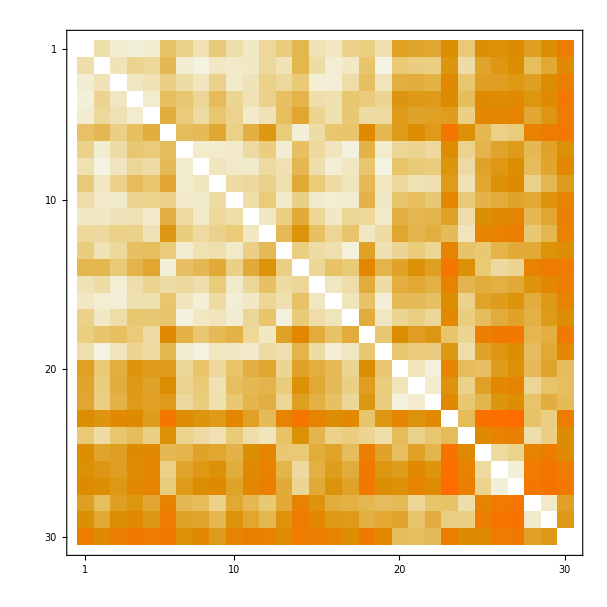

```mathematica
MatrixPlot[%]
```

```mathematica
Apply[distancefraction,allmemberlist ,{2}]//N
```

(0.000191663 | 0.0286536 | 0.0276953 | 0.0213704 | 0.0276953 | 0.00479157 | 0.0143747 | 0.0283661 | 0.00776234 | 0.0286536 | 0.0357451 | 0.0214662 | 0.00824149 | 0.00431241 | 0.0325827 | 0.0333493 | 0.0123622 | 0.0100623 | 0.0264494 | 0.0018208 | 0.00143747 | 0.00220412 | 0.0000958313 | 0.00881648 | 0.0000958313 | 0.000383325 | 0.0000958313 | 0.00105414 | 0.0000958313 | 0.
0.0286536 | 0.000191663 | 0.0308577 | 0.0151414 | 0.0194538 | 0.00517489 | 0.0330618 | 0.00565405 | 0.0333493 | 0.0319118 | 0.0357451 | 0.0259703 | 0.0325827 | 0.00431241 | 0.0288452 | 0.0311452 | 0.0357451 | 0.00737901 | 0.00287494 | 0.00881648 | 0.0111164 | 0.0100623 | 0.00105414 | 0.0288452 | 0.00143747 | 0.000383325 | 0.0000958313 | 0.00603737 | 0.0033541 | 0.0000958313
0.0276953 | 0.0308577 | 0.000191663 | 0.0358409 | 0.0283661 | 0.0100623 | 0.0288452 | 0.0358409 | 0.0123622 | 0.0319118 | 0.0308577 | 0.0123622 | 0.0214662 | 0.00881648 | 0.0276953 | 0.0249161 | 0.0286536 | 0.00603737 | 0.0308577 | 0.00344993 | 0.00287494 | 0.00373742 | 0.0000958313 | 0.00891231 | 0.00105414 | 0.00105414 | 0.000383325 | 0.00105414 | 0.000191663 | 0.
0.0213704 | 0.0151414 | 0.0358409 | 0.000191663 | 0.0361284 | 0.00479157 | 0.00891231 | 0.0219454 | 0.00574988 | 0.0172496 | 0.0283661 | 0.0143747 | 0.00479157 | 0.00392908 | 0.0286536 | 0.026162 | 0.00891231 | 0.00824149 | 0.0172496 | 0.00105414 | 0.000958313 | 0.00114998 | 0.000383325 | 0.00574988 | 0.0000958313 | 0.000479157 | 0.0000958313 | 0.00105414 | 0.0000958313 | 0.
0.0276953 | 0.0194538 | 0.0283661 | 0.0361284 | 0.000191663 | 0.00344993 | 0.00776234 | 0.0288452 | 0.00891231 | 0.015908 | 0.0319118 | 0.0325827 | 0.00603737 | 0.00220412 | 0.0151414 | 0.026162 | 0.00891231 | 0.0288452 | 0.0259703 | 0.00114998 | 0.00172496 | 0.0018208 | 0.00114998 | 0.0100623 | 0.000191663 | 0.000191663 | 0. | 0.00220412 | 0.000383325 | 0.
0.00479157 | 0.00517489 | 0.0100623 | 0.00479157 | 0.00344993 | 0.000191663 | 0.00574988 | 0.00440824 | 0.0033541 | 0.0101581 | 0.00239578 | 0.000383325 | 0.00776234 | 0.0281744 | 0.0288452 | 0.00891231 | 0.00737901 | 0.0000958313 | 0.00517489 | 0.00114998 | 0.000191663 | 0.00114998 | 0. | 0.000383325 | 0.00517489 | 0.0101581 | 0.00824149 | 0.000287494 | 0. | 0.
0.0143747 | 0.0330618 | 0.0288452 | 0.00891231 | 0.00776234 | 0.00574988 | 0.000191663 | 0.0361284 | 0.0319118 | 0.0319118 | 0.0259703 | 0.00824149 | 0.0276953 | 0.00479157 | 0.0194538 | 0.0374701 | 0.0167705 | 0.00325827 | 0.0361284 | 0.0172496 | 0.015908 | 0.0194538 | 0.000191663 | 0.015908 | 0.00469574 | 0.00143747 | 0.00114998 | 0.00517489 | 0.0018208 | 0.000383325
0.0283661 | 0.00565405 | 0.0358409 | 0.0219454 | 0.0288452 | 0.00440824 | 0.0361284 | 0.000191663 | 0.0374701 | 0.0319118 | 0.0319118 | 0.0259703 | 0.0283661 | 0.00517489 | 0.0264494 | 0.0281744 | 0.0333493 | 0.00891231 | 0.00287494 | 0.00737901 | 0.00776234 | 0.00824149 | 0.00105414 | 0.0259703 | 0.00172496 | 0.000383325 | 0.0000958313 | 0.00440824 | 0.00143747 | 0.000191663
0.00776234 | 0.0333493 | 0.0123622 | 0.00574988 | 0.00891231 | 0.0033541 | 0.0319118 | 0.0374701 | 0.000191663 | 0.0288452 | 0.0194538 | 0.0143747 | 0.0264494 | 0.00297077 | 0.00776234 | 0.0288452 | 0.0308577 | 0.00517489 | 0.0333493 | 0.0194538 | 0.0283661 | 0.026162 | 0.00114998 | 0.0283661 | 0.00220412 | 0.000383325 | 0.0000958313 | 0.0101581 | 0.00431241 | 0.00114998
0.0286536 | 0.0319118 | 0.0319118 | 0.0172496 | 0.015908 | 0.0101581 | 0.0319118 | 0.0319118 | 0.0288452 | 0.000191663 | 0.0286536 | 0.00776234 | 0.0319118 | 0.0101581 | 0.0319118 | 0.0311452 | 0.0276953 | 0.00373742 | 0.0357451 | 0.00737901 | 0.00603737 | 0.00891231 | 0.000191663 | 0.00881648 | 0.00392908 | 0.00287494 | 0.00172496 | 0.0033541 | 0.000574988 | 0.
0.0357451 | 0.0357451 | 0.0308577 | 0.0283661 | 0.0319118 | 0.00239578 | 0.0259703 | 0.0319118 | 0.0194538 | 0.0286536 | 0.000191663 | 0.0333493 | 0.0101581 | 0.00297077 | 0.0219454 | 0.0357451 | 0.0219454 | 0.0214662 | 0.0319118 | 0.00239578 | 0.00517489 | 0.00431241 | 0.0018208 | 0.0286536 | 0.0000958313 | 0.0000958313 | 0.0000958313 | 0.00517489 | 0.00220412 | 0.
0.0214662 | 0.0259703 | 0.0123622 | 0.0143747 | 0.0325827 | 0.000383325 | 0.00824149 | 0.0259703 | 0.0143747 | 0.00776234 | 0.0333493 | 0.000191663 | 0.00440824 | 0.000574988 | 0.00479157 | 0.0172496 | 0.00737901 | 0.0333493 | 0.0288452 | 0.00220412 | 0.00469574 | 0.00344993 | 0.00440824 | 0.0374701 | 0. | 0. | 0.0000958313 | 0.00891231 | 0.00431241 | 0.
0.00824149 | 0.0325827 | 0.0214662 | 0.00479157 | 0.00603737 | 0.00776234 | 0.0276953 | 0.0283661 | 0.0264494 | 0.0319118 | 0.0101581 | 0.00440824 | 0.000191663 | 0.0100623 | 0.0288452 | 0.026162 | 0.0160997 | 0.0018208 | 0.0283661 | 0.0172496 | 0.00824149 | 0.0219454 | 0.000191663 | 0.007954 | 0.00881648 | 0.00469574 | 0.00297077 | 0.00297077 | 0.000574988 | 0.000191663
0.00431241 | 0.00431241 | 0.00881648 | 0.00392908 | 0.00220412 | 0.0281744 | 0.00479157 | 0.00517489 | 0.00297077 | 0.0101581 | 0.00297077 | 0.000574988 | 0.0100623 | 0.000191663 | 0.0219454 | 0.007954 | 0.00881648 | 0.000191663 | 0.00431241 | 0.00172496 | 0.000383325 | 0.00105414 | 0. | 0.000383325 | 0.00881648 | 0.0259703 | 0.0151414 | 0.000287494 | 0.0000958313 | 0.0000958313
0.0325827 | 0.0288452 | 0.0276953 | 0.0286536 | 0.0151414 | 0.0288452 | 0.0194538 | 0.0264494 | 0.00776234 | 0.0319118 | 0.0219454 | 0.00479157 | 0.0288452 | 0.0219454 | 0.000191663 | 0.0333493 | 0.0286536 | 0.00287494 | 0.0288452 | 0.00344993 | 0.0033541 | 0.00325827 | 0.0000958313 | 0.00431241 | 0.00287494 | 0.00239578 | 0.0033541 | 0.000479157 | 0.000191663 | 0.0000958313
0.0333493 | 0.0311452 | 0.0249161 | 0.026162 | 0.026162 | 0.00891231 | 0.0374701 | 0.0281744 | 0.0288452 | 0.0311452 | 0.0357451 | 0.0172496 | 0.026162 | 0.007954 | 0.0333493 | 0.000191663 | 0.0374701 | 0.007954 | 0.0311452 | 0.00440824 | 0.00440824 | 0.00479157 | 0.000191663 | 0.0123622 | 0.00172496 | 0.00114998 | 0.000479157 | 0.00287494 | 0.000958313 | 0.0000958313
0.0123622 | 0.0357451 | 0.0286536 | 0.00891231 | 0.00891231 | 0.00737901 | 0.0167705 | 0.0333493 | 0.0308577 | 0.0276953 | 0.0219454 | 0.00737901 | 0.0160997 | 0.00881648 | 0.0286536 | 0.0374701 | 0.000191663 | 0.00297077 | 0.0333493 | 0.0151414 | 0.0100623 | 0.0219454 | 0.000191663 | 0.0111164 | 0.00574988 | 0.00287494 | 0.0018208 | 0.00325827 | 0.00114998 | 0.000191663
0.0100623 | 0.00737901 | 0.00603737 | 0.00824149 | 0.0288452 | 0.0000958313 | 0.00325827 | 0.00891231 | 0.00517489 | 0.00373742 | 0.0214662 | 0.0333493 | 0.0018208 | 0.000191663 | 0.00287494 | 0.007954 | 0.00297077 | 0.000191663 | 0.00891231 | 0.0000958313 | 0.00105414 | 0.00105414 | 0.00737901 | 0.0151414 | 0.0000958313 | 0. | 0. | 0.00431241 | 0.00239578 | 0.
0.0264494 | 0.00287494 | 0.0308577 | 0.0172496 | 0.0259703 | 0.00517489 | 0.0361284 | 0.00287494 | 0.0333493 | 0.0357451 | 0.0319118 | 0.0288452 | 0.0283661 | 0.00431241 | 0.0288452 | 0.0311452 | 0.0333493 | 0.00891231 | 0.000191663 | 0.00891231 | 0.00824149 | 0.0111164 | 0.000383325 | 0.0286536 | 0.00172496 | 0.000383325 | 0.000191663 | 0.00603737 | 0.0033541 | 0.
0.0018208 | 0.00881648 | 0.00344993 | 0.00105414 | 0.00114998 | 0.00114998 | 0.0172496 | 0.00737901 | 0.0194538 | 0.00737901 | 0.00239578 | 0.00220412 | 0.0172496 | 0.00172496 | 0.00344993 | 0.00440824 | 0.0151414 | 0.0000958313 | 0.00891231 | 0.000191663 | 0.0308577 | 0.0160997 | 0. | 0.00574988 | 0.00479157 | 0.00114998 | 0.000383325 | 0.00440824 | 0.00143747 | 0.00574988
0.00143747 | 0.0111164 | 0.00287494 | 0.000958313 | 0.00172496 | 0.000191663 | 0.015908 | 0.00776234 | 0.0283661 | 0.00603737 | 0.00517489 | 0.00469574 | 0.00824149 | 0.000383325 | 0.0033541 | 0.00440824 | 0.0100623 | 0.00105414 | 0.00824149 | 0.0308577 | 0.000191663 | 0.0361284 | 0.000479157 | 0.0143747 | 0.0018208 | 0. | 0.000191663 | 0.0219454 | 0.007954 | 0.00603737
0.00220412 | 0.0100623 | 0.00373742 | 0.00114998 | 0.0018208 | 0.00114998 | 0.0194538 | 0.00824149 | 0.026162 | 0.00891231 | 0.00431241 | 0.00344993 | 0.0219454 | 0.00105414 | 0.00325827 | 0.00479157 | 0.0219454 | 0.00105414 | 0.0111164 | 0.0160997 | 0.0361284 | 0.000191663 | 0. | 0.00891231 | 0.00431241 | 0.00105414 | 0.000479157 | 0.00737901 | 0.00344993 | 0.00440824
0.0000958313 | 0.00105414 | 0.0000958313 | 0.000383325 | 0.00114998 | 0. | 0.000191663 | 0.00105414 | 0.00114998 | 0.000191663 | 0.0018208 | 0.00440824 | 0.000191663 | 0. | 0.0000958313 | 0.000191663 | 0.000191663 | 0.00737901 | 0.000383325 | 0. | 0.000479157 | 0. | 0.000191663 | 0.00574988 | 0. | 0. | 0. | 0.007954 | 0.0100623 | 0.0000958313
0.00881648 | 0.0288452 | 0.00891231 | 0.00574988 | 0.0100623 | 0.000383325 | 0.015908 | 0.0259703 | 0.0283661 | 0.00881648 | 0.0286536 | 0.0374701 | 0.007954 | 0.000383325 | 0.00431241 | 0.0123622 | 0.0111164 | 0.0151414 | 0.0286536 | 0.00574988 | 0.0143747 | 0.00891231 | 0.00574988 | 0.000191663 | 0.0000958313 | 0.000287494 | 0. | 0.0286536 | 0.0101581 | 0.000479157
0.0000958313 | 0.00143747 | 0.00105414 | 0.0000958313 | 0.000191663 | 0.00517489 | 0.00469574 | 0.00172496 | 0.00220412 | 0.00392908 | 0.0000958313 | 0. | 0.00881648 | 0.00881648 | 0.00287494 | 0.00172496 | 0.00574988 | 0.0000958313 | 0.00172496 | 0.00479157 | 0.0018208 | 0.00431241 | 0. | 0.0000958313 | 0.000191663 | 0.0259703 | 0.015908 | 0. | 0. | 0.0000958313
0.000383325 | 0.000383325 | 0.00105414 | 0.000479157 | 0.000191663 | 0.0101581 | 0.00143747 | 0.000383325 | 0.000383325 | 0.00287494 | 0.0000958313 | 0. | 0.00469574 | 0.0259703 | 0.00239578 | 0.00114998 | 0.00287494 | 0. | 0.000383325 | 0.00114998 | 0. | 0.00105414 | 0. | 0.000287494 | 0.0259703 | 0.000191663 | 0.0213704 | 0. | 0. | 0.
0.0000958313 | 0.0000958313 | 0.000383325 | 0.0000958313 | 0. | 0.00824149 | 0.00114998 | 0.0000958313 | 0.0000958313 | 0.00172496 | 0.0000958313 | 0.0000958313 | 0.00297077 | 0.0151414 | 0.0033541 | 0.000479157 | 0.0018208 | 0. | 0.000191663 | 0.000383325 | 0.000191663 | 0.000479157 | 0. | 0. | 0.015908 | 0.0213704 | 0.000191663 | 0. | 0. | 0.
0.00105414 | 0.00603737 | 0.00105414 | 0.00105414 | 0.00220412 | 0.000287494 | 0.00517489 | 0.00440824 | 0.0101581 | 0.0033541 | 0.00517489 | 0.00891231 | 0.00297077 | 0.000287494 | 0.000479157 | 0.00287494 | 0.00325827 | 0.00431241 | 0.00603737 | 0.00440824 | 0.0219454 | 0.00737901 | 0.007954 | 0.0286536 | 0. | 0. | 0. | 0.000191663 | 0.0319118 | 0.0018208
0.0000958313 | 0.0033541 | 0.000191663 | 0.0000958313 | 0.000383325 | 0. | 0.0018208 | 0.00143747 | 0.00431241 | 0.000574988 | 0.00220412 | 0.00431241 | 0.000574988 | 0.0000958313 | 0.000191663 | 0.000958313 | 0.00114998 | 0.00239578 | 0.0033541 | 0.00143747 | 0.007954 | 0.00344993 | 0.0100623 | 0.0101581 | 0. | 0. | 0. | 0.0319118 | 0.000191663 | 0.00114998
0. | 0.0000958313 | 0. | 0. | 0. | 0. | 0.000383325 | 0.000191663 | 0.00114998 | 0. | 0. | 0. | 0.000191663 | 0.0000958313 | 0.0000958313 | 0.0000958313 | 0.000191663 | 0. | 0. | 0.00574988 | 0.00603737 | 0.00440824 | 0.0000958313 | 0.000479157 | 0.0000958313 | 0. | 0. | 0.0018208 | 0.00114998 | 0.000191663)

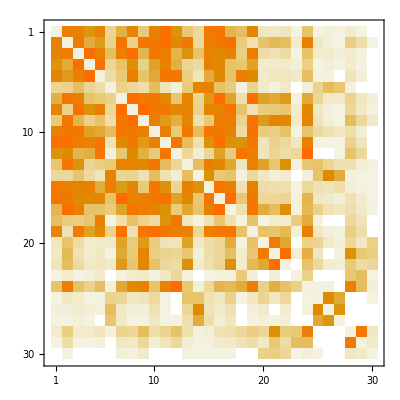

```mathematica
MatrixPlot[%]
```